```mathematica
(* Common *)
On[Assert]
comment[c_][val_]:=(Print[c]; val);
Second[xs_]:=xs[[2]];
atNotebook[path_]:=FileNameJoin[{NotebookDirectory[],path}];
$AssertFunction=Print["ASSERTION FAILED: "<>ToString[##]]&;
inGroupsOf[n_][lst_]:=Partition[lst,n,n,{1,1},{}];

sanityCheck[]:=
Map[Block[{h=#},
Print["Testing "<>ToString[h]];
Assert[m0[h]≥0,"Negative mass"]; (* Non-negative mass *)
Assert[Γ0[h]≥0,"Negative width"]; (* Non-negative width *)
(*Assert[Sum[dec[[2]],{dec,decays[h]}]==1.,"Incomplete branching ratios for "<>ToString[h]];*)
Assert[2isoSpin[h]∈Integers,"Isospin is not half-integer for "<>ToString[h]]; (* Half-integer isospin *)
Assert[idMask[h]≠0,"Particle without mask is in Pythia"];(*Pythia particles must have id mask*)
Map[Module[{hA,hB,jA,jB,jOut,lChan,inRange,outRange,mmin},
hA=#[[1,1]];hB=#[[1,2]];
jA=j@hA;jB=j@hB;jOut=j@h;lChan=#[[3]];
inRange=Range[Abs[jA-jB],Abs[jA+jB]];
outRange=Range[Abs[jOut-lChan],Abs[jOut+lChan]];
Assert[IntersectingQ[inRange,outRange],"Angular momenta inaccessible for "<>ToString[h]<>"-->"<>ToString[#[[1]]]]; (* Must be possible to conserve angular momentum *)
Assert[Γ0@hA>0.||Γ0@hB==0.,"Second particle is the resonance"];
mmin=Sum[minMass@out,{out,#[[1]]}];
Assert[mmin≤ m0@h,"Minimum mass of decay products is higher than particle mass for "<>ToString[h]<>"-->"<>ToString[#[[1]]]](* Particles cannot decay to products with higher rest mass *)
]&,decays[h]];
True
]&,pythiaEntries];

pythiaEntries={
N1440,N1520,N1535,N1650,N1675,N1680,N1700,N1710,N1720,N1875,N1880,N1895,N1900,N2060,N2100,N2120,N2190,N2220,N2250,
D1232,D1600,D1620,D1700,D1900,D1905,D1910,D1920,D1930,D1950,D2200,D2420,
L1405,L1520,L1600,L1670,L1690,L1800,L1810,L1820,L1830,L1890,L2100,L2110,
S1385,S1660,S1670,S1750,S1775,S1915,S1940,S2030,
X1530,X1820,X2030,O2012,O2250,
rho,sigma
(*,
rho,omega,f0980,Kstar,phi,K0star,a0980,f01370,K11270,a11260,
f1,f11510,K21430,a21320,f21270,f21525,K11400,b11235,h11170,h11380,Kstar1680,rho1465*)
};

(* Kinematic and helper functions *)
ClearAll[BR0]; ClearAll[BRsum];
fitRegge[s_,z_,y1_,y2_]:=z+0.308Log[s/28.998]^2+y1(1./s)^0.458-y2(1./s)^0.545;
fitHERA[p_,a_,b_,n_,c_,d_]:=a+b p^n+c Log[p]^2+d Log[p];
GeVInv2mb=0.38937966;
breitWigner[Γ0_,dm_]:=1/(2Pi)*Γ0/(dm^2+Γ0^2/4)
getDecay[hIn_,hOuts_]:=SelectFirst[decays[hIn],#[[1]]==hOuts&];
BRsum[h_]:=BRsum[h]=Sum[dec[[2]],{dec,decays[h]}];
BR0[hIn_,hOuts_]:=Block[{dec=getDecay[hIn,hOuts]},If[MissingQ[dec],0,dec[[2]]]]/BRsum[hIn];
isMeson[pi]=True;isMeson[pipi]=True;isMeson[eta]=True;isMeson[Ka]=True;
isMeson[h_]:=MemberQ[Ms,h];
decayAngularMomentum[hIn_,hOuts_]:=getDecay[hIn,hOuts][[3]];
decayProducts[particle_]:=First/@decays[particle];
minMass[particle_]:=
If[Γ0[particle]==0.,m0[particle],
0.05+Min@Select[#>0&]@Table[Total[minMass/@products],{products,decayProducts[particle]}]
];
maxMass[particle_]:=If[isMeson[particle],m0[particle]+5Γ0[particle],mMax[particle]];

pCMS[eCM_,mA_,mB_]:=
If[eCM≤mA+mB,0.,
Block[{s=eCM*eCM},
Sqrt[(s-(mA+mB)^2)(s-(mA-mB)^2)] / (2.eCM)
]
]
pLab[mA_,mB_,eCM_]:=If[eCM≤mA+mB,0,Sqrt[(eCM^2-(mA+mB)^2)(eCM^2-(mA-mB)^2)]/(2mB)];
pLabInv[mA_,mB_,pLab_]:=Sqrt[mA^2+mB^2+2mB Sqrt[mA^2+pLab^2]];

psSize[mDistribution_][eCM_,{hA_,hB_},lFac_]:=Module[{m0A,m0B},
m0A=m0[hA];m0B=m0[hB];
(* Zero resonances *)
If[Γ0[hA]==0.&&Γ0[hB]==0.,
If[eCM<m0A+m0B,Return[0],Return@(pCMS[eCM,m0A,m0B]^lFac)]
];

(* One resonance *)
If[Γ0[hA]==0.,
If[eCM<m0A+minMass@hB,Return[0],
Return@NIntegrate[pCMS[eCM,m0A,mB]^lFac mDistribution[hB,mB],{mB,minMass[hB],eCM-m0A}, PrecisionGoal->3,AccuracyGoal->10]
]];
If[Γ0[hB]==0.,(* Ensure hB is resonance *)
Return[psSize[mDistribution][eCM,{hB,hA},lFac]]];

(* Two resonances *)
If[eCM≤minMass@hA+minMass@hB,Return[0.]];
NIntegrate[pCMS[eCM,mA,mB]^lFac mDistribution[hA,mA]mDistribution[hB,mB],{mA,minMass[hA],eCM-minMass[hB]},{mB,minMass[hB],eCM-mA}]
];

a0[particle_,m_]:=breitWigner[Γ0@particle,(m-m0@particle)];
pMean0=psSize[a0];

ClearAll[BR];ClearAll[Γ];
Γ[hIn_,hOuts_,m_]:=Γ[hIn,hOuts,m]=Module[{br0,lChan,pRatio1,pRatio},
If[m≤Sum[minMass[h],{h,hOuts}],Return[0]];
br0=BR0[hIn,hOuts];
If[br0==0,Return[0]];
lChan=decayAngularMomentum[hIn,hOuts];

pRatio1=pMean[m,hOuts,2lChan+1]/pMean[m0@hIn,hOuts,2lChan+1];
pRatio=pMean[m,hOuts,2lChan]/pMean[m0@hIn,hOuts,2lChan];
If[pRatio1≤0||pRatio≤0,
Print["No available phase space for:",hIn->hOuts,m];
Return[0];
];

Return[br0 Γ0[hIn]* m0[hIn]/m * pRatio1 * 1.2/(1. + 0.2pRatio)];
]

Γ[h_,m_]:=Γ[h,m]=Sum[Γ[h,decs,m],{decs,decayProducts[h]}];
BR[hIn_,hOuts_,m_]:=Γ[hIn,hOuts,m]/Γ[hIn,m];

(* Define the mass distribution function and <p> *)

ClearAll[a];
a[particle_,m_Real]:=
Block[{mm=m},a[particle,mm]=If[Γ0[particle]==0.,Throw["In a: Singular mass distribution for "<>ToString[particle]],
If[minMass@particle<mm<maxMass@particle,breitWigner[Γ[particle,mm],(mm-m0@particle)]
,0]
]
];

pMean[eCM_,hOuts_,lFac_]:=psSize[a][eCM,hOuts,lFac];

strangeFactor[h_]:=1.-0.4*strangeness[h]/If[isMeson[h],2.,3.];

ClearAll[mCenter];
mCenter[h_]:=mCenter[h]=First@FindArgMax[a[h,m],{m,m0@h,m0@h-0.3,m0@h+0.3}];
```

```mathematica
sanityCheck[]
```

Testing N1440

Testing N1520

Testing N1535

Testing N1650

Testing N1675

Testing N1680

Testing N1700

Testing N1710

Testing N1720

Testing N1875

Testing N1880

Testing N1895

Testing N1900

Testing N2060

Testing N2100

Testing N2120

Testing N2190

Testing N2220

Testing N2250

Testing D1232

Testing D1600

Testing D1620

Testing D1700

Testing D1900

Testing D1905

Testing D1910

Testing D1920

Testing D1930

Testing D1950

Testing D2200

Testing D2420

Testing L1405

Testing L1520

Testing L1600

Testing L1670

Testing L1690

Testing L1800

Testing L1810

Testing L1820

Testing L1830

Testing L1890

Testing L2100

Testing L2110

Testing S1385

Testing S1660

Testing S1670

Testing S1750

Testing S1775

Testing S1915

Testing S1940

Testing S2030

Testing X1530

Testing X1820

Testing X2030

Testing O2012

Testing O2250

Testing rho

Testing sigma

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
pts=Monitor[
Table[{outs,Table[{m,Γ[N1535,outs,m]},{m,1.,2.,0.01}]},{outs,decayProducts[N1535]}],
ProgressIndicator[m,{1.,2.}]
];
ptsTot=Monitor[
Table[{m,Γ[N1535,m]},{m,1.,2.,0.01}],
ProgressIndicator[m,{1.,2.}]
];
```

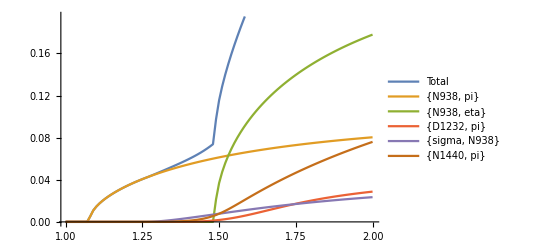

```mathematica
ListLinePlot[Second/@(Prepend[{"Total",ptsTot}]@pts),PlotLegends->ToString/@First/@(Prepend[{"Total",ptsTot}]@pts)]
```